# Homework 4

Wang Long	1101110160	Work in Mathematica 8.0.0

## Question 2

A new, bright, two--image gravitational lens has been found, with the following characteristics:
	-- Separation = 2.1”;
	-- zlens = 0.6;
	-- zsource = 2.2;
	-- Component A is 0.7” from the centre of the lensing galaxy;
	-- Component B is 1.4” from the centre.
Comparison with older observations indicates that there is a time delay of 1 year between the variability behaviour of components A and B.

### A Estimate the distance to the lensing galaxy.

Figure 1: Sketch of a typical gravitational lens system.

The Separation is 2.1’’ and Image A and B is 0.7’’ and 1.4’’ from center separately. This means A and B are at opposite directions respect with center thus A, B, source and lensing galaxy should be in the same plane. Treating lens galaxy as point mass, the source angle β from the lensing galaxy center can be calculated by equation:

β=θ-(4G M D_ds)/(c^2 D_D D_S)θ/(|θ|^2)=θ-θ_E^2 θ/(|θ|^2)

Input θ_1=1.4'' and θ_2=-0.7'', we get two equations and then can obtain β = 0.7, θ_E^2=0.98. 
	The we can calculate the time delay between two images as:

dt=1/c(√(Dd^2+ξ_l2^2) +√(Dds^2+(ξ_l2+ξ_s)^2)-√(Dd^2+ξ_l1^2)-√(Dds^2+(ξ_l1-ξ_s)^2))
=Dd √(1+θ2^2)+√(Dds^2+(Dd*θ2-(Dd+Dds)*β)^2)-Dd √(1+θ1^2)-√(Dds^2+(Dd*θ1-(Dd+Dds)*β)^2)
=Dd [√(1+θ2^2)-√(1+θ1^2)+1/zl(√(zs^2 (1+β^2)-2 zl zs(1+ β θ2)+zl^2 (1+θ2^2))-√(zs^2 (1+β^2)-2 zl zs(1+ β θ1)+zl^2 (1+θ1^2)))]

Here ξ_s is the distance between source and line-of-sight passing lensing galaxies.
	Input zl=0.6, zs=2.2 and θ, β and dt = 1yr we can then obtain lensing galaxy distance Dd ≃13Gpc.

#### Code

```mathematica
θ1=1.4arcsec;θ2=-0.7arcsec;zs=2.2;zl=0.6;c=1lyr/yr;
β=(β1/.Solve[{β1==1.4-θe2/1.4,β1==-0.7+θe2/0.7},{β1,θe2}][[1,1]])arcsec;
θe=(√(θe2/.Solve[{β1==1.4-θe2/1.4,β1==-0.7+θe2/0.7},{β1,θe2}][[1,2]]))arcsec;
dD[Dd_]=-Simplify[Dd √(1+θ1^2)+√(Dds^2+(Dd*θ1-(Dd+Dds)*β)^2)-Dd √(1+θ2^2)-√(Dds^2+(Dd*θ2-(Dd+Dds)*β)^2)/.{Dds->Dd(zs-zl)/zl,arcsec->1/3600*π/180.0},Dd>0];
Dl=Dd/.Solve[ dD[Dd]==c 1yr/.lyr->1/3.26163342/1*^9Gpc,Dd][[1,1]]
```

12.907 Gpc

### B What simplifying assumption do you need to make?

I need to assume the lensing galaxy is not extended source comparing to the system. And there are no other massive sources along the line-of-sight direction to the source and lensing galaxy.

## Question 3

A spherical cloud of ionized hydrogen with uniform density and of radius R is emitting Bremsstrahlung radiation in X rays. The total observed X--ray surface brightness (or intensity), integrated over frequency, at the centre of the cloud is SX = 10–12 erg cm–2 s–1 arcmin–2. The X--ray spectrum has a typical Bremsstrahlung shape with temperature kT = 7 keV. The microwave background radiation is also observed through the cloud at a frequency of 90 MHz (i.e., well into the Rayleigh– Jeans regime), and at the cloud centre it has an intensity which is lower than the average cosmic microwave background intensity by a fractional amount of 5× 10–5. The cloud is observed to have an angular radius on the sky of 3 arcmin.

Find the radius R and the distance to the cloud. You will need to do some background research to successfully tackle this exercise. You need to work out (or look up) the Sunyaev–Zel’dovich decrement as a function of electron density, the Bremsstrahlung’s emissivity integrated over frequency, and work out the cluster’s ion density.

Note: In the real cosmological case, with the cloud being a cluster of galaxies at some redshift z receding from us due to the expansion of the Universe, the X--ray surface brightness is reduced to below its true value by a factor (1+z)4, and the X--ray spectrum gets redshifted, showing an apparent temperature that is lower by a factor 1+z. The numbers given in this problem are typical values for a rich cluster at z ≅ 0.3, after these redshift effects have been corrected for.

### Answer

From Equation 2.5.4 and 2.5.7 in book written by Weinberg, 2008, we can get the Sunyaev-Zeldovich decrement as a function of electron density and electron temperature.

ΔT_γ/T_γ=-2 σ_T/(m_e c^2)∫ⅆl N_e[l]kT[l]

Since the observed frequency is in Rayleigh-Jeans regime and using Rayleigh-Jeans law I=2k T v^2/c^2 we can get

ΔI/I=ΔT_γ/T_γ

Assuming uniform temperature in the spherical cloud with uniform density and radius R, we then get

ΔI/I=-(4 σ_T k T N_e R)/(m_e c^2)

Input -ΔI / I = 5 × 10^-5, k T = 7 keV, σ_T=6.652448×10^-25 cm^-2, m_e=9.109534×10^-28 g, c=3×10^8 m/s, we get

N_e R=1.4×10^21 cm^2

From Equation 6.44 and 6.45 in book written by Hanjun You, 1998, we can get emissivity integrated over frequency as:

j[T]=(64/(3 √3))α_f r_0^2 c(c/OverBar[v_th])k T SOverBar[g_ff][T]=1.4×10^-27 T^(1/2)S g_ff[T](erg cm^-3 s^-1)
		g_ff[T]=∫_0^∞ OverBar[g_ff][T]e^-ξ ⅆξ, ξ=hv/kT
		S=∑N_e N_Z Z^2

For cloud of ionized hydrogen, Z=1 and N_e=N_Z. Since temperatue of this cloud kT=7keV, g_eff[T]≃1.2±10%. Then we can get

j[T]=1.68×10^-27 T^(1/2)N_e^2(erg cm^-3 s^-1)

The observed flux of the cloud:

F=(j V)/(4π D^2)=(j 4π R^3)/(3 4π D^2)=(j R^3)/(3 D^2)

Then the center surface brightness

S_X= F/(π θ^2)=(j R^3)/(3π θ^2 D^2)=(j R)/(3π)=1.5×10^-35 R T^(1/2)N_e^2 (erg cm^-2 s^-1 arcmin^-2)

Here A/Ω_0 is the area per solid angle seen from Earth. D is the cloud distance to Earth.

Input temperature T=8.11×10^7 K we get

S_X=1.4×10^-31 R N_e^2=10^-12 erg cm^-2 s^-1 arcmin^-2
		N_e^2 R=7.4×10^18 cm^2

Together with N_e R≃1.4×10^21 cm^2 , we can derive electon density and radius:

N_e=0.0054 cm^-3
		R=2.6×10^23 cm

Then the cloud distance to Earth can be estimated as:

D=R/θ=95Mpc

#### Code

```mathematica
dI=5*^-5;
T=7 keV/k;
θ=3arcmin;
σT=6.652448*^-25 cm^-2;
me=9.109534×10^-31 kg;
c=3*^8m/s;
k=1.3806504*^-23 J Kk^-1;
"NeR="
ner=((dI me c^2)/(4 σT k T)/.{keV->1*^3*1.6*^-19kg m^2/s^2})[[1]] cm^-2
"j="
(*j=Simplify[((8π e^6 Ne^2/(3me c^3 h)√((k Te)/me)/.{e->1.6*^-19* (8.987551787*^9 *1*^7erg m)^(1/2),h->6.62606896*^-34 *1*^7erg s,J->1*^7erg})/.kg->1*^7erg s^2/m^2)/.m->100cm,{kg>0,m>0,s>0,cm>0}][[1]]*)
j[Te_,Ne_]=1.68×10^-27(Te/Kk)^(1/2)(Ne/cm^-3)^2(erg cm^-3 s^-1)
"Fx="
Fx[Te_,Ne_]=j[Te,Ne] R^3/(3 Dd^2)
"Sx="
Sx[Te_,Ne_]=(j[Te,Ne]R)/(3π (180*60/π)^2 arcmin^2)
"Ne2R="
ne2r=Ne^2 R(1*^-12erg cm^-2 s^-1 arcmin^-2/Sx[T,Ne])/.keV->1*^3*1.6*^-19J
"Ne"
ne=ne2r/ner
"R"
r=ner/ne 
"D"
d=r/θ/.{arcmin->1/60/180*π,cm->1/3.08567756*^24Mpc}
```

NeR=

(1.37546×10^21)/cm^2

j=

(1.68×10^-27 cm^3 erg Ne^2 √(Te/Kk))/s

Fx=

(5.6×10^-28 cm^3 erg Ne^2 R^3 √(Te/Kk))/(Dd^2 s)

Sx=

(1.50831×10^-35 cm^3 erg Ne^2 R √(Te/Kk))/(arcmin^2 s)

Ne2R=

(7.3611×10^18)/cm^5

Ne

0.00535172/cm^3

R

2.57013×10^23 cm

D

95.4461 Mpc

```mathematica
Clear[j]
```

```mathematica
Simplify[(64/(3 √3))αf r0^2 k Te c(c/vth)/.{αf->1/137,r0->2.8179402894*^-15m,vth->√(8k/π me)}/.J->kg m^2/s^2/.m->100cm,{cm>0,kg>0,s>0,Kk>0}]
```

(1.5675 cm^5 Te)/(√Kk s^3)

## Question 4

The method of ‘Monte Carlo simulation’ is frequently used to solve problems that are too complex for analytical analysis. If we observe stars down to a fixed apparent brightness, we do not get a fair mixture of all stars in the sky, but we are biased to include more of the most luminous stars (because of the effect of observational uncertainties). This is called the Malmquist bias. In this problem you will “observe” stars at different distances down to some limiting magnitude.

	a. Your model sky consists of G--type stars in regions A (85 pc < d < 95 pc), B (95 pc < d < 105 pc) and C (105 pc < d < 115 pc). If the density is uniform and you have 10 stars in region B, how many do you have in regions A and C? Round up to the nearest integer. Hint: the volumes sampled by shells of different radii will be different. For simplicity, let all of the stars in region A be at 90 pc, in region B at 100 pc, and at region C at 110 pc.

	b. G stars do not all have the same luminosity; if the variation corresponds to 0.3 magnitudes, what fractional change in luminosity does this correspond to? For each of your stars, roll a die, note the number you rolled, N1, and give your star an absolute V--band magnitude, MV = MV, + 0.3 × (N1 – 3.5). If you prefer to write a computer program, you can use more stars, place them randomly in space, and choose the absolute magnitudes from a Gaussian distribution with mean MV, and variance 0.3 mag.

	c. To “observe” your stars, use a “telescope” that can “see” only stars brighter than apparent magnitude mV = 9.8; these are your “observed” sample stars. How different is their mean absolute magnitude, <MV>, from the entire sample (including the ones “not observed”)? What is the average distance of the stars in the “observed” sample? Suppose you assumed that your sample stars each had the same luminosity as the average of the entire sample and then calculated their distances from their apparent magnitudes; what would you find for their average distance? In which sense would you make an error?

	d. Metal--poor main--sequence stars are bluer for a given luminosity, so they must be fainter at a given spectral type. If the star’s fraction by weight of heavy elements is Z, then ΔMV ≅ –0.87 log(Z/Z). For each of your stars, roll the die again, note the number, N2, and calculate a new absolute magnitude assuming that the star has Z = (N2 +0.5)/6Z. If you prefer to use a computer program here as well, randomly select Z between 0 and Z. For the “observed” sample of stars, calculate the average Z of those that fall in region A. Are these, on average, more or less metal--rich than the stars from region C that are in your “observed” sample?

### Code

```mathematica
dL={10^(-0.3/2.5)-1,10^(0.3/2.5)-1}//N;
intg=Integrate[r^2 Sin[t],{t,0,θ},{f,0,ϕ},{r,#[[1]],R}]/Integrate[r^2 Sin[t],{t,0,θ},{f,0,ϕ},{r,#[[1]],#[[2]]}]&/@{{85,95},{95,105},{105,115}};
```

```mathematica
ClearAll[r,θ,ϕ]
```

```mathematica
datatable=Table[{(Random[]/intg[[j,1]]-intg[[j,2,1]])^(1/3),Random[]*2π,ArcCos[1-2Random[]],RandomVariate[NormalDistribution[4.83,0.3]],Random[]},{j,3},{i,1000}];
dataxyz=Table[Cases[datatable[[i]],{r_,f_,t_,m_,z_}->{{{r Sin[t]Cos[f],r Sin[t]Sin[f],r Cos[t]}},m,m+5Log10[r]-5,{r,f,t},z,m-0.87Log10[z],m-0.87Log10[z]+5Log10[r]-5}],{i,3}];
rangem={Max@#,Max@#-Min@#}&@Flatten@dataxyz[[All,All,2]];
plotdata:=ListPointPlot3D[Flatten[dataxyz[[All,All,1]],1],BoxRatios->1,AxesLabel->{"x[pc]","y[pc]","z[pc]"},PlotLabel->"Figure 1: Star spatial distribution",PlotStyle->Flatten[Table[RGBColor[(rangem[[1]]-dataxyz[[j,i,2]])/rangem[[2]],0,(j-1)/1.2],{j,3},{i,Length@datatable[[1]]}],1],ImageSize->400]
datasel=Table[Select[dataxyz[[i]],#[[3]]≤9.8&],{i,3}];
dataselz=Table[Select[dataxyz[[i]],#[[7]]≤9.8&],{i,3}];
```

```mathematica
ranger=Table[{Min@#,Max@#}&@dataxyz[[i,All,4,1]],{i,3}];
funmean[dataset_,a_,b_]:=Table[{Mean@dataset[[i,All,a,b]],Mean@dataxyz[[i,All,a,b]]},{i,3}]
funmean[dataset_,a_]:=Table[{Mean@dataset[[i,All,a]],Mean@dataxyz[[i,All,a]]},{i,3}]
fundev[dataset_,a_]:=Table[{StandardDeviation@dataset[[i,All,a]],StandardDeviation@dataxyz[[i,All,a]]},{i,3}]
fundev[dataset_,a_,b_]:=Table[{StandardDeviation@dataset[[i,All,a,b]],StandardDeviation@dataxyz[[i,All,a,b]]},{i,3}]
meanr=funmean[datasel,4,1];
varr=fundev[datasel,4,1];
meanm=funmean[datasel,2];
varm=fundev[datasel,2];
meanz=funmean[dataselz,5];
varz=fundev[dataselz,5];
label={"A","B","C"};
plotdataref=Grid[Table[{Graphics[{PointSize[Large],RGBColor[(rangem[[1]]-meanm[[i,2]])/rangem[[2]],0,(i-1)/1.2],Point[{0,0}]},ImageSize->10],"⟨M_V⟩ in Region "~~label[[i]]},{i,3}],Alignment->Center,Frame->True];
datasel2=Table[Cases[datasel[[i]],{x_,M_,m_,r_,z_,Mc_,mc_}->{x,M,m,r,10^((m-meanm[[i,2]]+5)/5)}],{i,3}];
meanestr=Table[Mean@datasel2[[i,All,5]],{i,3}];
varstr=Table[StandardDeviation@datasel2[[i,All,5]],{i,3}];
funmix[da_,db_,index_,intr_,pre_,pree_]:=Prepend[Piecewise[{{SetPrecision[#1,pre],#1<100},{SetPrecision[#1,pre+1],#1≥100}}]±SetPrecision[#2,pree]&@@@Transpose@{da[[All,index]],db[[All,index]]},intr]
funmix[da_,db_,intr_,pre_]:=Prepend[Piecewise[{{SetPrecision[#1,pre],#1<100},{SetPrecision[#1,pre+1],#1≥100}}]±SetPrecision[#2,pre-1]&@@@Transpose@{da,db},intr]
restable:="Table 1: Calculated parameters\n"Grid[{{"Pars","A[85-95pc]","B[95-105pc]","C[105-115pc]"},Prepend[Length/@datasel,"N_OS"]}~Join~(funmix[meanr,varr,#1,#2,4,3]&@@@{{1,"⟨r⟩_OS"},{2,"⟨r⟩_ES"}})~Join~(
funmix[meanm,varm,#1,#2,3,2]&@@@{{1,"⟨M_V⟩_OS"},{2,"⟨M_V⟩_ES"}})~Join~{funmix[meanestr,varstr,"⟨r⟩_EstS",4]},Frame->All]
Mhist:=Histogram[Table[datasel2[[i,All,2]],{i,3}],ChartLegends->{"A","B","C"},AxesLabel->{"M_V","Number"},PlotLabel->"Figure 2-B: Absolute Magnitude distribution of observed sample",ImageSize->400]
Mhiste:=Histogram[Table[dataxyz[[i,All,2]],{i,3}],ChartLegends->{"A","B","C"},AxesLabel->{"M_V","Number"},PlotLabel->"Figure 2-A: Absolute Magnitude distribution of entire sample",ImageSize->400]
rvsr:=ListPlot[Table[Transpose@{datasel2[[i,All,4,1]],datasel2[[i,All,5]]},{i,3}],Epilog->First@Plot[x,{x,85,115},PlotStyle->Black],AxesLabel->{"r[pc]","r_Est[pc]"},PlotLabel->"Figure 3: Estimated distance vs. original distance"]
restablez:="Table 2: Calculated parameters for heavy elements abundance\n"Grid[{{"Pars","A[85-95pc]","B[95-105pc]","C[105-115pc]"},Prepend[Length/@dataselz,"N_OS"]}~Join~(funmix[meanz,varz,#1,#2,4,4]&@@@{{1,"⟨Z⟩_OS"},{2,"⟨Z⟩_ES"}}),Frame->All]
zhist:=Histogram[Table[dataselz[[i,All,5]],{i,3}],ChartLegends->{"A","B","C"},AxesLabel->{"Z","Number"},PlotLabel->"Figure 4-B: heavy elements abundance distribution of observed sample",ImageSize->400]
zhiste:=Histogram[Table[dataxyz[[i,All,5]],{i,3}],ChartLegends->{"A","B","C"},AxesLabel->{"Z","Number"},PlotLabel->"Figure 4-A: heavy elements abundance distribution of entire sample",ImageSize->400]
```

### A

Since it’s uniform distribution, number of stars N_R∝V. A, B and C have volume:

V_A=4/3 π (R_1^3-R_2^3)=4/3 π(95^3-85^3)pc^3=(973000 π)/3 pc^3
		V_B=4/3 π (R_2^3-R_3^3)=4/3 π(105^3-95^3)pc^3=(1201000 π)/3 pc^3
		V_C=4/3 π(R_2^3-R_3^3)=4/3 π(115^3-105^3)pc^3=(1453000 π)/3 pc^3

So the number ratio of A, B and C is:

n_A:n_B:n_C=V_A:V_B:V_C=973:1201:1453≃9:10:13

### B

For the same distance star, let G-type star luminosity to be L_G, absolute magnitude M_G, thus we will have

(M_G±0.3)-M_G=-2.5log[(f_G±Δf_G)/f_G]=-2.5log[((f_G±Δf_G) 4π D^2)/(f_G 4π D^2)]=-2.5log[(L_G±ΔL_G)/L_G]

Then the fractional change in luminosity

(±ΔL_G)/L_G=10^(∓0.3/2.5)-1≃{-0.24
+0.32

I generate 1000 stars in each regions, the spatial distribution is shown in Figure 1. Here I set the mean absolute V band magnitude of G star to be the same as Sun: 4.83 mag.

### C

Use Monte Carlo samples generated above, I then calculated average distances, average absolute magnitude and estimated average distances assuming same luminosities of obseved samples and entire samples in three regions separately. All results are listed in Table 1.

From Table 1 we can see that ⟨M_V⟩_OS are smaller than ⟨M_V⟩_ES about 0.2 mag and the ⟨r⟩_OS are smaller than ⟨r⟩_ES about 0.5-1 pc. This means we are easier to observe close and bright stars. The big difference is the ⟨r⟩_EstS comparing with ⟨r⟩_OS. The former is much smaller than the latter, especially in larger distance region like C.

Figure 2 and 3 shows the reasons of this error. When we estimated the distance of stars, we assuming the sample has a mean absolute magnitude of 4.83 mag. But the observed magnitude limit causes selection effect, which ignore the faint stars at large distance that we cannot observe. Thus the real mean absolute magnitudes are smaller than the assuming mean value of 4.83 mag (Figure 2). This bias is worse at larger distance region. Therefore, we underestimate the intrinsic luminosity of the observed samples, thus it results in the underestimation of distance. Besides, from Figure 3 we can see that there is a cut of estimated distance which is the observation distance limit for G stars. It’s obviouse we cannot avoid underestimation of distance.

#### Plot

```mathematica
Column[{plotdata,plotdataref}]
```

-Graphics3D-
-Graphics- | ⟨M_V⟩ in Region A
-Graphics- | ⟨M_V⟩ in Region B
-Graphics- | ⟨M_V⟩ in Region C

Note: Different color means different regions and Absolute Magnitude.

```mathematica
restable
```

Table 1: Calculated parameters
 Pars | A[85-95pc] | B[95-105pc] | C[105-115pc]
N_OS | 746 | 445 | 221
⟨r⟩_OS | 89.91±2.79 | 99.6±2.97 | 109.29±2.72
⟨r⟩_ES | 90.19±2.79 | 100.2±2.97 | 110.11±2.87
⟨M_V⟩_OS | 4.7±0.23 | 4.59±0.18 | 4.45±0.14
⟨M_V⟩_ES | 4.82±0.3 | 4.84±0.3 | 4.84±0.3
⟨r⟩_EstS | 85.28±8.58 | 88.76±6.9 | 91.33±5.19

Note: Errors are calculated by standard deviation of samples. Suffix ‘OS’ means observed sample, ‘ES’ means entire sample, ‘EstS’ means estimated values assuming same intrinsic luminosity for all observed stars.

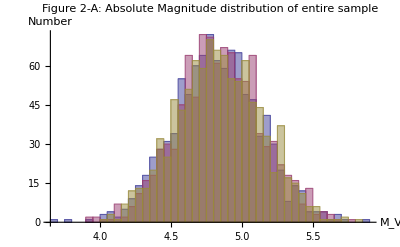
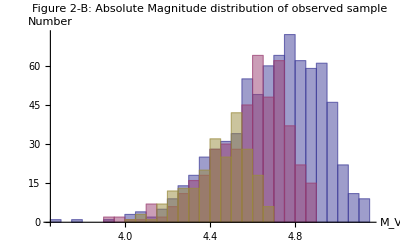
-Graphics--Graphics- | A
-Graphics- | B
-Graphics- | C
-Graphics--Graphics- | A
-Graphics- | B
-Graphics- | C

```mathematica
Column[{Mhiste,Mhist}]
```

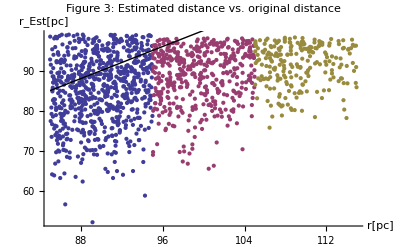

```mathematica
rvsr
```

Notes: different colors represent different regions. Black lines means r_Est=r.

### D

After I added heavy elements abundance influence, the result of observed abundance ⟨Z⟩_OS and entire sample abundance ⟨z⟩_ES are listed in Table 2. We can see that the number of observed stars are much less than before. The result shows the overestimated Z and a trend of higher Z at larger distance region. Since metal-poor main sequence star is fainter at a given spectral type, it’s reasonable to see more metal-rich stars with flux-limit observation. In Figure 4, we can see that the distribution of observed Z is not normal distributed. At high Z region, there are more stars.

#### Plot

```mathematica
restablez
```

Table 2: Calculated parameters for heavy elements abundance
 Pars | A[85-95pc] | B[95-105pc] | C[105-115pc]
N_OS | 395 | 167 | 67
⟨z⟩_OS | 0.6865±0.2182 | 0.7286±0.195 | 0.7808±0.1663
⟨z⟩_ES | 0.5185±0.2877 | 0.485±0.2883 | 0.4902±0.2898

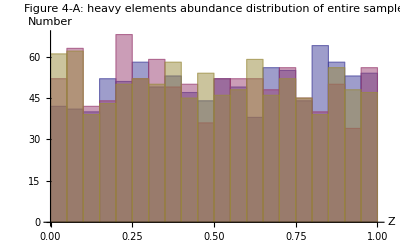
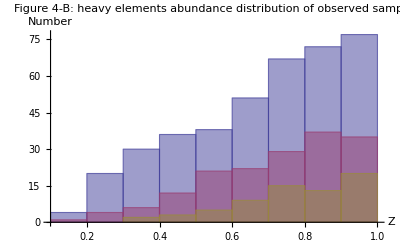
-Graphics--Graphics- | A
-Graphics- | B
-Graphics- | C
-Graphics--Graphics- | A
-Graphics- | B
-Graphics- | C

```mathematica
Column[{zhiste,zhist}]
```